VQCDThermo basic tutorial.

This notebook contains the minimal tutorial needed to getting started in computing the black hole solutions to the VQCD equations of motion, and extracting some simple plots and observables from them. You should read the paper arxiv:1312.5199 in order to have some idea on what we’re computing here, and you should have reasonable familiarity with Mathematica syntax.

We assume here that you have already installed the package so that Mathematica can find it. See INSTALLATION.md in the repository for instructions. First we need to load the package:

```mathematica
Needs["VQCDThermo`"]
```

Then we need to define some potentials:

```mathematica
xf = 1.;
pots = DefineJKPotIKappaMod[xf]
```

{VQCDThermo`VQCDCore`Private`Vg$591,VQCDThermo`VQCDCore`Private`Vf$591,VQCDThermo`VQCDCore`Private`κ$591,VQCDThermo`VQCDCore`Private`κ$591}

The function above defines the potentials used in the finite T, finite μ -paper. I gave xf a numerical value 1., since I’ll be wanting to do some calculations.

There are other potential functions in the file VQCDCore.m, and following their example you should also be able to define you own potentials. Caveat: ω ≠ κ is not supported at the moment.

The object pots contains a list of the potential functions, specifically {Vg, Vf, κ, ω} defined as pure functions. Let’s just check with Vg that we can for example plot it. This is of course not necessary for just using the potentials for calculations.

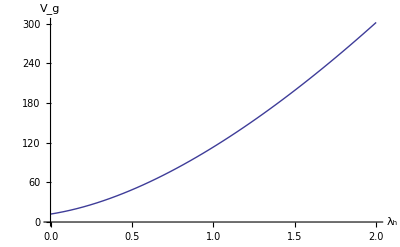

```mathematica
Vg = pots[[1]];
Plot[Vg[λ], {λ, 0, 2}, AxesLabel-> {"λ_h", "V_g"}]
```

Now we’re ready to compute a solution. There are certain limits to the parameter values which lead to a solution, see the paper for more details. Here we of course pick ones which work.

Start off with a zero mass, zero tachyon solution, and just arbitrarily pick nt = 1:

```mathematica
λh = 1.;
τh = 0.;
nt = 1.;
sol1 = SolveAndScaleVQCDBH[λh, τh, nt, pots]
```

{VQCDThermo`VQCDCore`Private`q1$1863,VQCDThermo`VQCDCore`Private`f1$1863,VQCDThermo`VQCDCore`Private`λ1$1863,VQCDThermo`VQCDCore`Private`τd1$1863,VQCDThermo`VQCDCore`Private`τ1$1863,2.79621×10^-9,160.,1.50476,1.89035,True,{3.,3.5},1.40102}

Then let’s take some numbers out of it. Everything is in units of Λ. Note that the code calls the 0-component of the gauge field A, as in A0, as opposed to Φ in the paper.

```mathematica
T = TemperatureFromSols[sol1]
{A0, μ} = AAndMuFromSols[sol1, nt, pots]
s = s4G5FromSols[sol1] (*Entropy density*)
n = 1/(4Pi)ntildeFromSols[sol1, nt] (*Charge density, in units of Subscript[ℒ, A]*)
```

0.33441

{Function[A$,VQCDThermo`VQCDCore`Private`Afunc$1865[A$]-VQCDThermo`VQCDCore`Private`Afunc$1865[2.79621×10^-9]],0.0976116}

0.293495

0.0233556

We can also plot the field configurations. It’s a bit clearer to assign names to the fields before starting to work. Unfortunately, using for example λ as a name for the λ-field can cause conflicts in any further attempts to solve the system, so append s for solution to all field names.

All the fields and components of the metric are returned as functions of A = log(b). The radial coordinate z as a function of A can be obtained from the function zFromSols.

The warnings are due to a well known Mathematica bug (fixed in v9): http://mathematica.stackexchange.com/questions/5986/why-does-loglinearplot-sample-its-argument-outside-the-specified-domain

InterpolatingFunction::dmval: Input value {-19.6945} lies outside the range of data in the interpolating function. Extrapolation will be used.

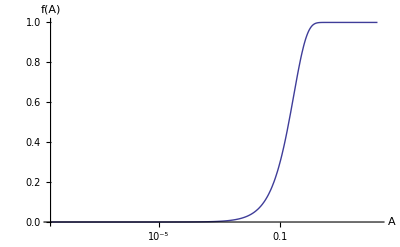

InterpolatingFunction::dmval: Input value {-19.6945} lies outside the range of data in the interpolating function. Extrapolation will be used.

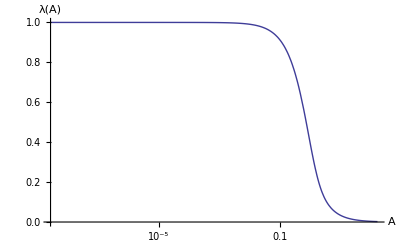

InterpolatingFunction::dmval: Input value {-19.6945} lies outside the range of data in the interpolating function. Extrapolation will be used.

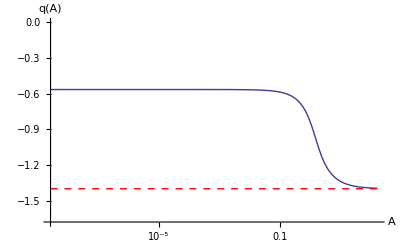

InterpolatingFunction::dmval: Input value {-19.6945} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-19.6945} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-19.189} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-19.189} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-18.6835} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {-18.6835} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction :: dprec will be suppressed during this calculation.

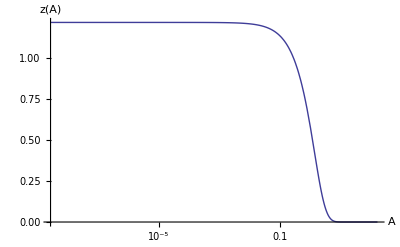

InterpolatingFunction::dmval: Input value {-19.6945} lies outside the range of data in the interpolating function. Extrapolation will be used.

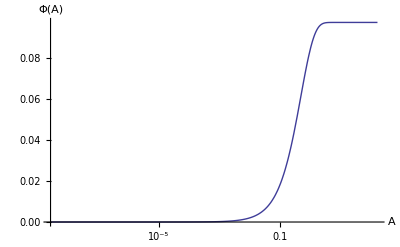

```mathematica
λs = λFromSols[sol1];
fs = fFromSols[sol1];
qs = qFromSols[sol1];
τs = τFromSols[sol1];
{Amin, Amax} = ARangeFromSols[sol1];
zs = zFromSols[sol1];

{bcoefs, ell} = bCoefsFromPotential[pots]; (*Extract Subscript[ℒ, UV] to check the correct asymptotic of q*)

LogLinearPlot[fs[A], {A, Amin, Amax}, AxesLabel-> {"A", "f(A)"}]
LogLinearPlot[λs[A], {A, Amin, Amax}, AxesLabel -> {"A", "λ(A)"}]
LogLinearPlot[{qs[A], -ell}, {A, Amin, Amax}, AxesLabel -> {"A", "q(A)"}, PlotStyle-> {Automatic, {Red, Dashed}}, PlotRange-> {Min[-ell, qs[Amax]]*1.2, 0}]

LogLinearPlot[zs[A], {A, Amin, Amax}, AxesLabel-> {"A", "z(A)"}]

LogLinearPlot[A0[A], {A, Amin, Amax},  AxesLabel -> {"A", "Φ(A)"}]
```

Let’s then try looking at finite τ solutions:

```mathematica
λh = 2.;
τh = 1.;
nt = 1.;
sol2a = SolveAndScaleVQCDBH[λh, τh, nt, pots]
```

{VQCDThermo`VQCDCore`Private`q1$8861,VQCDThermo`VQCDCore`Private`f1$8861,VQCDThermo`VQCDCore`Private`λ1$8861,VQCDThermo`VQCDCore`Private`τd1$8861,VQCDThermo`VQCDCore`Private`τ1$8861,3.4564×10^-9,160.,1.82058,1.7186,True,{3.,3.5},1.40102}

Check the mass

```mathematica
QuarkMass[sol2a, pots]
```

0.765969

All good, but we’d usually rather fix the mass, and determine τh from that. This will take a minute or two:

```mathematica
mq = 0;
τh = τhFromQuarkMass[mq, λh, nt, pots]
```

0.358875

Now we can use that value to compute a solution. Note that the τh we gained is of course only correct for this specific set of λh, nt, and needs to be recomputed for other values. This is the primary effort in terms of computation time for the thermo solutions.

Let’s now compute the solution corresponding to that.

```mathematica
sol2 = SolveAndScaleVQCDBH[λh, τh, nt, pots];
```

The corresponding observables are

```mathematica
T = TemperatureFromSols[sol2]
{A0, μ} = AAndMuFromSols[sol2, nt, pots]
s = s4G5FromSols[sol2] (*Entropy density*)
n = 1/(4Pi)ntildeFromSols[sol2, nt] (*Charge density, in units of Subscript[ℒ, A]*)
mqactual = QuarkMass[sol2, pots] (*The actual mass*)
```

0.144465

{Function[A$,VQCDThermo`VQCDCore`Private`Afunc$13672[A$]-VQCDThermo`VQCDCore`Private`Afunc$13672[1.68442×10^-10]],0.0350483}

0.0076709

0.000610431

-2.68342×10^-11

Note that the mass is indeed of order 10^-11.

Let’s see how the configurations appear:

InterpolatingFunction::dmval: Input value {-22.5039} lies outside the range of data in the interpolating function. Extrapolation will be used.

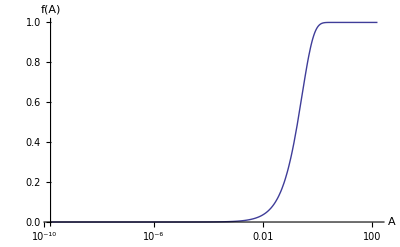

InterpolatingFunction::dmval: Input value {-22.5039} lies outside the range of data in the interpolating function. Extrapolation will be used.

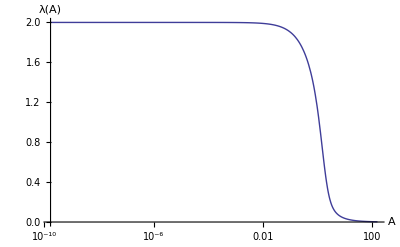

InterpolatingFunction::dmval: Input value {-22.5039} lies outside the range of data in the interpolating function. Extrapolation will be used.

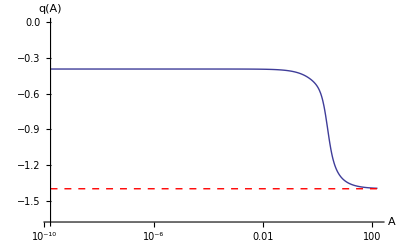

InterpolatingFunction::dmval: Input value {-22.5039} lies outside the range of data in the interpolating function. Extrapolation will be used.

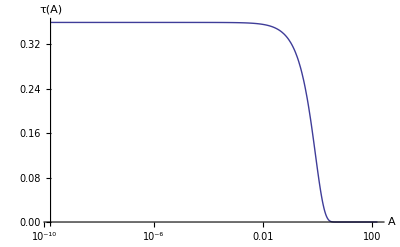

InterpolatingFunction::dmval: Input value {-22.5039} lies outside the range of data in the interpolating function. Extrapolation will be used.

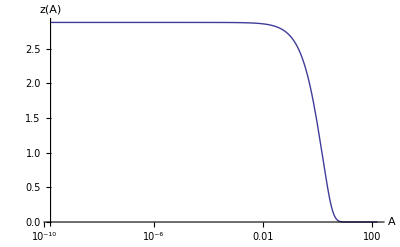

InterpolatingFunction::dmval: Input value {-22.5039} lies outside the range of data in the interpolating function. Extrapolation will be used.

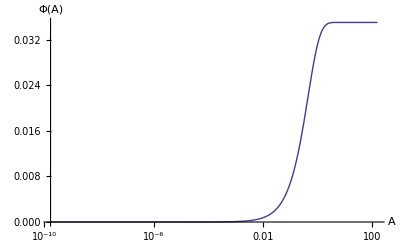

```mathematica
λs = λFromSols[sol2];
fs = fFromSols[sol2];
qs = qFromSols[sol2];
τs = τFromSols[sol2];
{Amin, Amax} = ARangeFromSols[sol2];
zs = zFromSols[sol2];

{bcoefs, ell} = bCoefsFromPotential[pots]; (*Extract Subscript[ℒ, UV] to check the correct asymptotic of q*)

LogLinearPlot[fs[A], {A, Amin, Amax}, AxesLabel-> {"A", "f(A)"}]
LogLinearPlot[λs[A], {A, Amin, Amax}, AxesLabel -> {"A", "λ(A)"}]
LogLinearPlot[{qs[A], -ell}, {A, Amin, Amax}, AxesLabel -> {"A", "q(A)"}, PlotStyle-> {Automatic, {Red, Dashed}}, PlotRange-> {Min[-ell, qs[Amax]]*1.2, 0}]
LogLinearPlot[τs[A], {A, Amin, Amax}, AxesLabel-> {"A", "τ(A)"}]

LogLinearPlot[zs[A], {A, Amin, Amax}, AxesLabel-> {"A", "z(A)"}]

LogLinearPlot[A0[A], {A, Amin, Amax},  AxesLabel -> {"A", "Φ(A)"}]
```

Finally, let’s see how some of these components can be combined to find, as an exercise, a point very near to the AdS2 -limit, with μ = 0.507, that is, very close to T = 0 chiral restoration transition.

Find by finding the exact position of the AdS2 -point. This is of course given in the paper, so this here is just an example.

```mathematica
ntcritfun = ntCritical[pots]; (*This returns the limiting curve nt(la) where Veff = 0*)
λhcrit = λhcr /. FindRoot[ntcritfun'[λhcr], {λhcr, 1.5, 0.5}, Method-> "Brent"] (**)
ntcrit = ntcritfun[λhcrit]
nt = ntcrit - 10^-2
```

1.10794

12.2947

12.2847

We’ll be looking at 10^-2 away from the AdS2 -point

Then define a function which returns just the μ given λh

```mathematica
μNearAdS2[λh_?NumericQ] := Module[{sol}, 
sol = SolveAndScaleVQCDBH[λh, 0, nt, pots];
AAndMuFromSols[sol, nt, pots][[2]] (*Index 2 is μ*)
]
```

Now, we need to find an interval in λh where to look for this. It would be easy enough to guess, but let’s do it systematically.

FindNumLimit is a helper function in NumericsExtra, which does a binary search for the point where a function ceases to have a numeric value (as judged by NumericQ).

```mathematica
λhmax = FindNumLimit[μNearAdS2[λhv], {λhv, λhcrit, 2.}]
λhmin = FindNumLimit[μNearAdS2[λhv], {λhv, 0.01, λhcrit}]
```

1.16078

1.05126

Check that this interval brackets the value of μ we’re looking for. Then we can just use Mathematica’s standard FindRoot with Brent’s method to find the λ_h we want:

```mathematica
μNearAdS2[λhmax]
μNearAdS2[λhmin]
```

0.0583225

2.85402

It does.

```mathematica
λhμc = λhv /. FindRoot[μNearAdS2[λhv] == 0.507, {λhv, λhmin, λhmax}, Method -> "Brent"]
```

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

1.15969

The FindRoot warning just means that this is as close as we can get without using more than machine precision. Compute the actual solution, the observables, and plot the configurations.

```mathematica
solμc = SolveAndScaleVQCDBH[λhμc, 0, nt, pots]

T = TemperatureFromSols[solμc]
{A0, μ} = AAndMuFromSols[solμc, nt, pots]
s = s4G5FromSols[solμc] (*Entropy density*)
n = 1/(4Pi)ntildeFromSols[solμc, nt] (*Charge density, in units of Subscript[ℒ, A]*)
```

{VQCDThermo`VQCDCore`Private`q1$21439,VQCDThermo`VQCDCore`Private`f1$21439,VQCDThermo`VQCDCore`Private`λ1$21439,VQCDThermo`VQCDCore`Private`τd1$21439,VQCDThermo`VQCDCore`Private`τ1$21439,1.19407×10^-12,160.,3.7826,0.0128843,True,{3.,3.5},1.40102}

0.0000239733

{Function[A$,VQCDThermo`VQCDCore`Private`Afunc$21440[A$]-VQCDThermo`VQCDCore`Private`Afunc$21440[1.19407×10^-12]],0.506999}

0.0184768

0.0180628

InterpolatingFunction::dmval: Input value {-27.453} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-27.453} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-26.7891} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-26.7891} and/or the interpolation grid is insufficient to compute the value.

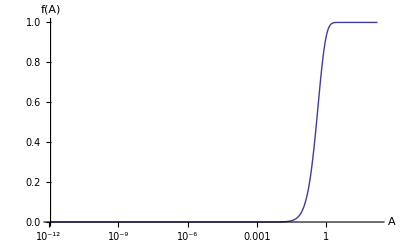

InterpolatingFunction::dmval: Input value {-27.453} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-27.453} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-26.7891} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-26.7891} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-26.1253} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {-26.1253} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction :: dprec will be suppressed during this calculation.

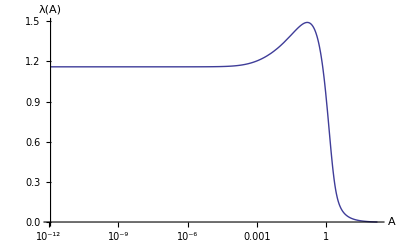

InterpolatingFunction::dmval: Input value {-27.453} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-27.453} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-26.7891} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-26.7891} and/or the interpolation grid is insufficient to compute the value.

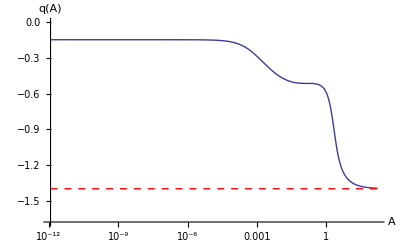

InterpolatingFunction::dmval: Input value {-27.453} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-27.453} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-26.7891} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-26.7891} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-26.1253} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {-26.1253} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction :: dprec will be suppressed during this calculation.

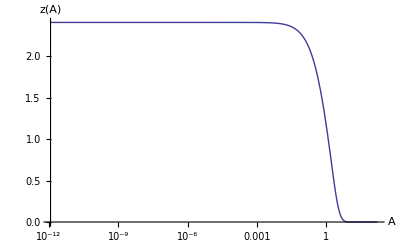

InterpolatingFunction::dmval: Input value {-27.453} lies outside the range of data in the interpolating function. Extrapolation will be used.

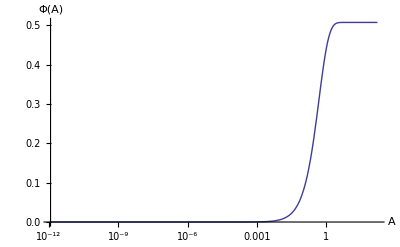

```mathematica
λs = λFromSols[solμc];
fs = fFromSols[solμc];
qs = qFromSols[solμc];
τs = τFromSols[solμc];
{Amin, Amax} = ARangeFromSols[solμc];
zs =zFromSols[solμc];

{bcoefs, ell} = bCoefsFromPotential[pots]; (*Extract Subscript[ℒ, UV] to check the correct asymptotic of q*)

LogLinearPlot[fs[A], {A, Amin, Amax}, AxesLabel-> {"A", "f(A)"}]
LogLinearPlot[λs[A], {A, Amin, Amax}, AxesLabel -> {"A", "λ(A)"}, PlotRange-> All]
LogLinearPlot[{qs[A], -ell}, {A, Amin, Amax}, AxesLabel -> {"A", "q(A)"}, PlotStyle-> {Automatic, {Red, Dashed}}, PlotRange-> {Min[-ell, qs[Amax]]*1.2, 0}]

LogLinearPlot[zs[A], {A, Amin, Amax}, AxesLabel-> {"A", "z(A)"}]

LogLinearPlot[A0[A], {A, Amin, Amax},  AxesLabel -> {"A", "Φ(A)"}]
```

Here’s how to plot, for example, λ(z):

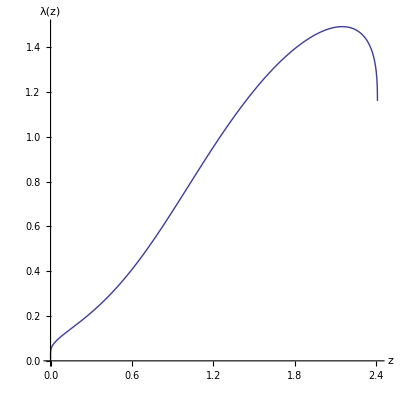

```mathematica
ParametricPlot[{zs[A], λs[A]}, {A, Amin, 50}, AspectRatio -> 1, PlotPoints-> 1500, PlotRange-> {{0, zs[Amin]}, All}, AxesLabel-> {"z", "λ(z)"}]
```

That’s all for now, folks! Stay tuned for the full thermo tutorial!